```mathematica
(* Gaussian sensing: Kitaev chain*)

(*a1,a2,...,an,a1d,...and -> x1,x2...,xn,p1,...pn*)
QT[N1_]:=Module[{i,j,Matrix},
Matrix=0*IdentityMatrix[2*N1];
For[i=1,i<=N1,i++,
Matrix[[i,i]]=1;
Matrix[[i,N1+i]]=1;
Matrix[[i+N1,i]]=-ⅈ;
Matrix[[i+N1,N1+i]]=ⅈ;
];
Matrix/√2
]

AMatrix[N1_,g_,ϕb_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[i!=j && Abs[i-j]==1,
If[i<j,A[[i,j]]=g*Exp[-ⅈ*ϕb],
A[[i,j]]=-g*Exp[ⅈ*ϕb]
];
];
]
];
A
]

BMatrix[N1_,g_,ϕb_,χ_,ϕχ_, m_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[ Abs[i-j]==1,
If[i<j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=g*Exp[-ⅈ*ϕb],A[[i,j]]=χ*Exp[-ⅈ*ϕχ]]];
If[i>j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=g*Exp[-ⅈ*ϕb],A[[i,j]]=χ*Exp[-ⅈ*ϕχ]]];
];
];
];
A
]


BosonicKitaevChain[N1_,g_,ϕb_,χ_,ϕχ_,m_]:=Module[{},
A=AMatrix[N1,g,ϕb];
B=BMatrix[N1,g,ϕb,χ,ϕχ, m];
m1=Join[A,B,2];
m2=Join[Conjugate[B],Conjugate[A],2];
assump=g>=0&&χ>=0&&ϕb∈Reals&&ϕχ∈Reals;
$Assumptions=assump;
Simplify[Join[m1,m2]]
]


GenerateA[N1_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[i==j,A[[i,j]]=-ⅈ*Subscript[ω, i],
If[i<j,A[[i,j]]=Subscript[g, i,j]*Exp[-ⅈ*Subscript[ϕ, b,i,j]],
A[[i,j]]=-Subscript[g, j,i]*Exp[ⅈ*Subscript[ϕ, b,j,i]]
];
];
]
];
A
]


GenerateB[N1_,m_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[i==j,If[m!={}&& IntersectingQ[{i},m],A[[i,j]]=Subscript[ω, i]*Exp[-ⅈ*Subscript[ϕ, s,i]],A[[i,j]]=Subscript[ξ, i]*Exp[-ⅈ*Subscript[ϕ, s,i]]]];
If[i<j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=Subscript[g, i,j]*Exp[-ⅈ*Subscript[ϕ, t,i,j]],A[[i,j]]=Subscript[χ, i,j]*Exp[-ⅈ*Subscript[ϕ, t,i,j]]]];
If[i>j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=Subscript[g, j,i]*Exp[-ⅈ*Subscript[ϕ, t,j,i]],A[[i,j]]=Subscript[χ, j,i]*Exp[-ⅈ*Subscript[ϕ, t,j,i]]]];
];
];
A
]

BQH[N1_,m_]:=Module[{A,B,m1,m2,assump},
A=GenerateA[N1];
B=GenerateB[N1,m];
m1=Join[A,B,2];
m2=Join[Conjugate[B],Conjugate[A],2];
assump=hui∈Reals;
For[i=1,i<=N1,i++,
assump=assump&&Subscript[ω, i]∈Reals&&Subscript[ξ, i]∈Reals&&Subscript[ϕ, s,i]∈Reals;
For[j=i,j<=N1,j++,
If[i!= j,assump=assump&&Subscript[g, i,j]∈Reals&&Subscript[χ, i,j]∈Reals&&Subscript[ϕ, t,i,j]∈Reals&&Subscript[ϕ, b,i,j]∈Reals;]
]];
$Assumptions=assump;
Simplify[Join[m1,m2]]
]

ZeroPhase[Nmodes_]:=Module[{i,j,phases},
phases={};
For[i=1,i<=Nmodes,i++,
phases=phases~Join~{Subscript[ϕ, s,i]->0};
For[j=i,j<=Nmodes,j++,
If[i!= j,phases=phases~Join~{Subscript[ϕ, t,i,j]->0,Subscript[ϕ, b,i,j]->0};]
]];
phases
]

killSPDC[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}],(*kill all xis*)Table[Subscript[ξ,i]->0,{i,1,N1}],(*kill all g_{i,j}*)Flatten@Table[Subscript[g,i,j]->0,{i,1,N1},{j,i+1,N1}],(*kill all chi except pairwise (2j-1,2j)*)Flatten@Table[If[j==i+1&&OddQ[i],Subscript[χ,i,j]->χ,Subscript[χ,i,j]->0],{i,1,N1},{j,i+1,N1}]];

killSPDCBS[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}],(*kill all xis*)Table[Subscript[ξ,i]->0,{i,1,N1}],Flatten@Table[If[j==i+1&&OddQ[i],Subscript[g,i,j]->g,Subscript[g,i,j]->0],{i,1,N1},{j,i+1,N1}],Flatten@Table[If[j==i+1&&OddQ[i],Subscript[χ,i,j]->χ,Subscript[χ,i,j]->0],{i,1,N1},{j,i+1,N1}]];

SPDCBS2[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}],(*kill all xis*)Table[Subscript[ξ,i]->0,{i,1,N1}],Flatten@Table[If[j==i+1,Subscript[g,i,j]->g,Subscript[g,i,j]->0],{i,1,N1},{j,i+1,N1}],Flatten@Table[If[j==i+1&&OddQ[i],Subscript[χ,i,j]->χ,Subscript[χ,i,j]->0],{i,1,N1},{j,i+1,N1}]];

(* with a phase *)
SPDCBS3[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}],(*kill all xis*)Table[Subscript[ξ,i]->0,{i,1,N1}],Flatten@Table[If[j==i+1,Subscript[g,i,j]->I g,Subscript[g,i,j]->0],{i,1,N1},{j,i+1,N1}],Flatten@Table[If[j==i+1&&OddQ[i],Subscript[χ,i,j]->-I χ,Subscript[χ,i,j]->0],{i,1,N1},{j,i+1,N1}]];


killomega[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}]];
killxi[N1_]:=Join[Table[Subscript[ξ,i]->0,{i,1,N1}]];
killg[N1_]:=Flatten[Table[Subscript[g,i,j]->0,{i,1,N1},{j,i+1,N1}]];
killchi[N1_]:=Flatten[Table[Subscript[χ,i,j]->0,{i,1,N1},{j,i+1,N1}]];


CovarBasis[N1_]:= Module[{i,j,A},
A=0*IdentityMatrix[2*N1];
For[i=1,i<=N1,i++,
A[[2i-1,i]]=1;
A[[2i,N1+i]]=1
];
A]



QFIperPhoton[Nmodes_,g_,χ_]:=Module[{EOM,DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{1/4 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]/.ϕ->0]//FullSimplify,2 D[λ,ϕ].Inverse[Σout/.ϕ->0].D[λ,ϕ]/.ϕ->0//FullSimplify,1/4 (Tr[Σout]-2 Nmodes)+1/2 Transpose[λ].λ//FullSimplify}
]


QFIperPhotonAnal[Nmodes_,g_,χ_]:=Module[{EOM,DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes//FullSimplify,2 D[λ,ϕ].Inverse[Σout/.ϕ->0].D[λ,ϕ]/.ϕ->0//FullSimplify,1/4 (Tr[Σout]-2 Nmodes)+1/2 Transpose[λ].λ//FullSimplify}
]

QFInoDisp[Nmodes_,g_,χ_]:=Module[{EOM,DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t];
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]];
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar];
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];
(1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes)/(1/4 (Tr[Σout]-2 Nmodes))//FullSimplify
]


LeadingOrderCheck[cov_,disp_,n_,Nmodes_]:=Module[{M,d,G,EOM,DM,DMq,CovForm,DispForm,nForm},
M=Nmodes;
d=Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
EOM=BosonicKitaevChain[Nmodes,χ,ϕb=0,χ,ϕχ=0,{}]//FullSimplify;
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
DMq=CovarBasis[Nmodes].DM.Transpose[CovarBasis[Nmodes]];

CovForm=Tr[1/2 1/((M-1)!)^4 MatrixPower[DMq,M-1].G.MatrixPower[DMq,M-1].MatrixPower[Transpose[DMq],M-1].Transpose[G].MatrixPower[Transpose[DMq],M-1]]//FullSimplify;
Print["leading order covariant ",CovForm];
Print[Coefficient[cov,t^(4M-4)]==CovForm//FullSimplify];

DispForm=(2 1)/((M-1)!)^4 d.MatrixPower[Transpose[DMq],M-1].Transpose[G].MatrixPower[Transpose[DMq],M-1].MatrixPower[DMq,M-1].G.MatrixPower[DMq,M-1].d//FullSimplify;
Print["leading order displacement ",DispForm];
Print[Coefficient[disp,t^(4M-4)]==DispForm//FullSimplify];

nForm=1/(4 ((M-1)!)^2)(Tr[MatrixPower[DMq,M-1].MatrixPower[Transpose[DMq],M-1]]+2 d.MatrixPower[Transpose[DMq],M-1].MatrixPower[DMq,M-1].d)//FullSimplify;
Print["leading order mean photon number  ",nForm];
Print[Coefficient[n,t^(2M-2)]==nForm//FullSimplify];
]


QFIperPhotonBQH[Nmodes_,EOM_]:=Module[{DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{1/4 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]/.ϕ->0]//FullSimplify,2 D[λ,ϕ].Inverse[Σout/.ϕ->0].D[λ,ϕ]/.ϕ->0//FullSimplify,1/4 (Tr[Σout]-2 Nmodes)+1/2 Transpose[λ].λ//FullSimplify}
]


FnNormal[Nmodes_,g_,χ_,t_]:=Module[{},
λ=Table[2 Sqrt[χ^2-g^2] Cos[(k π)/(Nmodes+1)],{k,1,Nmodes}];
x=Table[((χ-g)/(χ+g))^(k/2) Sin[(h k π)/(Nmodes+1)]//Simplify,{k,1,Nmodes},{h,1,Nmodes}];
y=Table[((χ+g)/(χ-g))^(k/2) Sin[(h k π)/(Nmodes+1)]//Simplify,{h,1,Nmodes},{k,1,Nmodes}];
tr=Tr[(2/(Nmodes+1))^4 ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@{-Transpose[y].MatrixExp[-DiagonalMatrix[λ]t].Transpose[x].x.MatrixExp[-DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[-DiagonalMatrix[λ ] t].Transpose[x].x.MatrixExp[-DiagonalMatrix[λ ] t].y,-x.MatrixExp[DiagonalMatrix[λ ] t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ ] t].Transpose[x].x.MatrixExp[DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ]t].Transpose[x]}]]]//N;

nout=1/4 Tr[(2/(Nmodes+1))^2 ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@{x.MatrixExp[-DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[-DiagonalMatrix[λ ] t].Transpose[x],x.MatrixExp[DiagonalMatrix[λ ] t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ ] t].Transpose[x]}]]]-Nmodes/2//N;

Fcov=-1/2 tr-Nmodes;
Fcov/nout
]
```

{-1/2,-1/2}

{-0.820156,-0.179844}

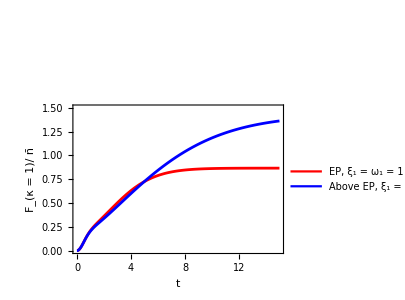

```mathematica
Clear[κ]
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Subscript[ξ, 1]=1;
Subscript[ω, 1]=1;


(* EP*)
Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
tmax=15;
int=Integrate[κ  MatrixExp[DM (t-s)].MatrixExp[Transpose[DM] (t-s)],{s,0,t}]//FullSimplify;
S=MatrixExp[DM t];
Σin=S.Transpose[S]+int;
n=1/4 (Tr[Σin]-2 Nmodes)//FullSimplify;
μsq=1/Det[Σin];
Fk=1/2 Tr[Inverse[Σin].D[Σin,κ].Inverse[Σin].D[Σin,κ]]/(1+μsq);
Fx=1/2 Tr[Inverse[Σin].D[Σin,κ].Inverse[Σin].D[Σin,κ]]/(1+μsq);
κ=1;
Eigenvalues[DM]
plt1=Plot[{Evaluate[Fk]/n},{t,0,tmax},PlotRange->All,PlotStyle->Red,PlotLegends->Placed[LineLegend[{Red,Blue},{"EP, ξ_1 = ω_1 = 1","Above EP, ξ_1 = 1.05, ω_1 = 1"},LabelStyle->{FontSize->10},LegendMargins->{{2,2},{2,2}},Spacings->{0.4,0.3},LegendFunction->(Framed[#,Background->White,FrameStyle->Black,FrameMargins->3]&)
],{Right,Bottom}]];



Clear[κ]
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Subscript[ξ, 1]=1.05;
Subscript[ω, 1]=1;


(* non EP *)
Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
int=Integrate[κ  MatrixExp[DM (t-s)].MatrixExp[Transpose[DM] (t-s)],{s,0,t}]//FullSimplify;
S=MatrixExp[DM t];
Σin=S.Transpose[S]+int;
n=1/4 (Tr[Σin]-2 Nmodes)//FullSimplify;
μsq=1/Det[Σin];
Fk=1/2 Tr[Inverse[Σin].D[Σin,κ].Inverse[Σin].D[Σin,κ]]/(1+μsq);
κ=1;
Eigenvalues[DM]
plt2=Plot[{Evaluate[Fk]/n},{t,0,tmax},PlotRange->All,PlotStyle->Blue];

Show[plt1,plt2,Frame->True,PlotRange->{0,1.5},Axes->None,FrameTicksStyle->Directive[FontSize->15],AspectRatio->1,FrameLabel->{Style["t",18,Italic,FontFamily->"Arial"],Style[TraditionalForm["F_(κ = 1)/"Overscript["n","_"]],18,Italic,FontFamily->"Arial"]},FrameStyle->Directive[Black,Thickness[0.006]],ImageSize->300,Epilog->{Text[Style["→ 6.93",14,Purple,FontFamily->"Arial",Bold],{18,6.7}],Text[Style[TraditionalForm["→ 8"],14,Red,FontFamily->"Arial",Bold],{18,7.7}],Text[Style[" → 5.33",14,Blue,FontFamily->"Arial",Bold],{17.5,5.1}]}]
```

```mathematica
Fkn/.{κ->1,ξ1->1,ω1->1}//N
Fkn/.{κ->1,ξ1->1.05,ω1->1}//N
Fkn/.{κ->1,ξ1->Sqrt[5]/2,ω1->1}//N
```

0.866667

1.42749

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

Unset::norep: Assignment on Subscript for ξ_1 not found.

$Failed

Unset::norep: Assignment on Subscript for ω_1 not found.

$Failed

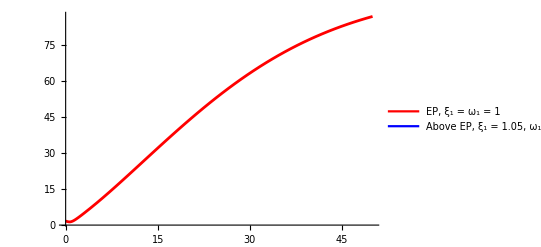

```mathematica
Clear[κ]
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
κ=1;
ω1=1;


(* EP*)
Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes]/.{Subscript[ξ, 1]->ξ1,Subscript[ω, 1]->ω1};
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
tmax=50;
int=Integrate[κ  MatrixExp[DM (t-s)].MatrixExp[Transpose[DM] (t-s)],{s,0,t}]//FullSimplify;
S=MatrixExp[DM t];
Σin=S.Transpose[S]+int;
n=1/4 (Tr[Σin]-2 Nmodes)//FullSimplify;
μsq=1/Det[Σin];

Fx=1/(2n) Tr[Inverse[Σin].D[Σin,ξ1].Inverse[Σin].D[Σin,ξ1]]/(1+μsq);


plt1=Plot[{Evaluate[Fx]/.ξ1->1.1},{t,0,tmax},PlotRange->All,PlotStyle->Red,PlotLegends->Placed[LineLegend[{Red,Blue},{"EP, ξ_1 = ω_1 = 1","Above EP, ξ_1 = 1.05, ω_1 = 1"},LabelStyle->{FontSize->10},LegendMargins->{{2,2},{2,2}},Spacings->{0.4,0.3},LegendFunction->(Framed[#,Background->White,FrameStyle->Black,FrameMargins->3]&)
],{Right,Bottom}]]
```

Unset::norep: Assignment on Subscript for ξ_1 not found.

$Failed

Unset::norep: Assignment on Subscript for ω_1 not found.

$Failed

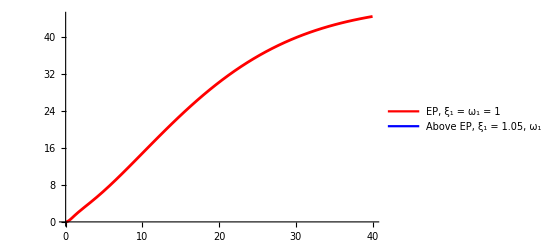

-Graphics-

```mathematica
Clear[κ,ω1,ξ1]
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
κ=1;
ξ1=1;


(* EP*)
Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes]/.{Subscript[ξ, 1]->ξ1,Subscript[ω, 1]->ω1};
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
tmax=40;
int=Integrate[κ  MatrixExp[DM s].MatrixExp[Transpose[DM] s],{s,0,t}]//FullSimplify;
S=MatrixExp[DM t];
Σin=S.Transpose[S]+int;
n=1/4 (Tr[Σin]-2 Nmodes)//FullSimplify;
μsq=1/Det[Σin];

Fw=1/(2n) Tr[Inverse[Σin].D[Σin,ω1].Inverse[Σin].D[Σin,ω1]]/(1+μsq);


plt1=Plot[{Evaluate[Fw]/.ω1->0.9},{t,0,tmax},PlotRange->All,PlotStyle->Red,PlotLegends->Placed[LineLegend[{Red,Blue},{"EP, ξ_1 = ω_1 = 1","Above EP, ξ_1 = 1.05, ω_1 = 1"},LabelStyle->{FontSize->10},LegendMargins->{{2,2},{2,2}},Spacings->{0.4,0.3},LegendFunction->(Framed[#,Background->White,FrameStyle->Black,FrameMargins->3]&)
],{Right,Bottom}]]
```

```mathematica
Clear[ξ1,ω1,κ]
EOM=BQH[Nmodes,{}]/.ZeroPhase[Nmodes]/.{Subscript[ξ, 1]->ξ1,Subscript[ω, 1]->ω1}/.κ->0;
MatrixExp[DM t].MatrixExp[Transpose[DM] t]//FullSimplify//MatrixForm
Integrate[MatrixExp[DM s].MatrixExp[Transpose[DM] s],{s,0,t}]//FullSimplify//MatrixForm

n=1/4 (Tr[Σin]-2 Nmodes);
μsq=1/Det[Σin];

Fw=1/(2n) Tr[Inverse[Σin].D[Σin,ω1].Inverse[Σin].D[Σin,ω1]]/(1+μsq);


DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
ξ1=ω1;
MatrixExp[DM t].MatrixExp[Transpose[DM] t]//FullSimplify//MatrixForm
Integrate[MatrixExp[DM s].MatrixExp[Transpose[DM] s],{s,0,t}]//FullSimplify//MatrixForm


n=1/4 (Tr[Σin]-2 Nmodes);
μsq=1/Det[Σin];

Fw=1/(2n) Tr[Inverse[Σin].D[Σin,ω1].Inverse[Σin].D[Σin,ω1]]/(1+μsq)//FullSimplify
```

((ⅇ^(-t κ) (-ω1^2+ξ1^2 Cosh[2 t √(ξ1^2-ω1^2)]+ξ1 √(ξ1^2-ω1^2) Sinh[2 t √(ξ1^2-ω1^2)]))/(ξ1^2-ω1^2) | -(2 ⅇ^(-t κ) ξ1 ω1 Sinh[t √(ξ1^2-ω1^2)]^2)/(ξ1^2-ω1^2)
-(2 ⅇ^(-t κ) ξ1 ω1 Sinh[t √(ξ1^2-ω1^2)]^2)/(ξ1^2-ω1^2) | -(ⅇ^(-t κ) (ω1^2-ξ1^2 Cosh[2 t √(ξ1^2-ω1^2)]+ξ1 √(ξ1^2-ω1^2) Sinh[2 t √(ξ1^2-ω1^2)]))/(ξ1^2-ω1^2))

$Aborted

(1+2 t ω1 (1+t ω1) | -2 t^2 ω1^2
-2 t^2 ω1^2 | 1+2 t ω1 (-1+t ω1))

(t+t^2 ω1+(2 t^3 ω1^2)/3 | -2/3 t^3 ω1^2
-2/3 t^3 ω1^2 | t-t^2 ω1+(2 t^3 ω1^2)/3)

1/ω1^2-10/(κ^2+2 ω1^2)+16/(κ^2+4 ω1^2)

```mathematica
(* steady-state analytical *)
Clear[ξ1,ω1,κ]
$Assumptions={Subscript[ξ, 1],Subscript[ω, 1],κ}∈Reals;
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes]/.{Subscript[ξ, 1]->ξ1,Subscript[ω, 1]->ω1};
"EOM is"
EOM//MatrixForm
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];

"DM is"
DM//FullSimplify//MatrixForm

"DM eigenvalues are"
DM//Eigenvalues//FullSimplify

"Stability threshold is"
Solve[-κ/2+√(Subscript[ξ, 1]^2-Subscript[ω, 1]^2)==0,κ]//FullSimplify[Assuming[{Subscript[ξ, 1],Subscript[ω, 1],κ}∈Reals,#]]&

"SS covariance matrix"
Σin=LyapunovSolve[DM ,Transpose[DM],-κ IdentityMatrix[2]]//FullSimplify;
Σin//FullSimplify//MatrixForm


"Mean photon number is"
n=1/4 (Tr[Σin]- 2 Nmodes)//FullSimplify

"Purity"
μsq=1/Det[Σin]//FullSimplify

"QFI is"
Fw=1/2 Tr[Inverse[Σin].D[Σin,ω1].Inverse[Σin].D[Σin,ω1]]/(1+μsq)//FullSimplify

"QFI per photon"
Fwn=Fw/n//FullSimplify

"QFI per at EP"
Fwn=Fw/n/.ξ1->ω1//FullSimplify



"QFI per photon at threshold"
Fwn/.κ->2 √(ξ1^2-ω1^2)//FullSimplify
Fwn/.κ->0//FullSimplify
```

Unset::norep: Assignment on Subscript for ξ_1 not found.

$Failed

Unset::norep: Assignment on Subscript for ω_1 not found.

$Failed

EOM is

(-κ/2-ⅈ ω1 | ξ1
ξ1 | -κ/2+ⅈ ω1)

DM is

(-κ/2+ξ1 | ω1
-ω1 | -κ/2-ξ1)

DM eigenvalues are

{-κ/2-√((ξ1-ω1) (ξ1+ω1)),-κ/2+√((ξ1-ω1) (ξ1+ω1))}

Stability threshold is

{{κ→2 √(ξ_1^2-ω_1^2)}}

SS covariance matrix

(1+(2 ξ1 (κ+2 ξ1))/(κ^2-4 ξ1^2+4 ω1^2) | -(4 ξ1 ω1)/(κ^2-4 ξ1^2+4 ω1^2)
-(4 ξ1 ω1)/(κ^2-4 ξ1^2+4 ω1^2) | (κ^2-2 κ ξ1+4 ω1^2)/(κ^2-4 ξ1^2+4 ω1^2))

Mean photon number is

(2 ξ1^2)/(κ^2-4 ξ1^2+4 ω1^2)

Purity

1-(4 ξ1^2)/(κ^2+4 ω1^2)

QFI is

(8 ξ1^2 (κ^4-4 κ^2 (ξ1^2-2 ω1^2)+16 ω1^2 (ξ1^2+ω1^2)))/((κ^2+4 ω1^2) (κ^2-4 ξ1^2+4 ω1^2)^2 (κ^2-2 ξ1^2+4 ω1^2))

QFI per photon

(4 (κ^4-4 κ^2 (ξ1^2-2 ω1^2)+16 ω1^2 (ξ1^2+ω1^2)))/((κ^2+4 ω1^2) (κ^2-4 ξ1^2+4 ω1^2) (κ^2-2 ξ1^2+4 ω1^2))

QFI per at EP

4 (4/κ^2-7/(κ^2+2 ω1^2)+4/(κ^2+4 ω1^2))

QFI per photon at threshold

(2 (ξ1^4-ξ1^2 ω1^2+2 ω1^4))/(ξ1^2 (2 ξ1^4-3 ξ1^2 ω1^2+ω1^4))

Power::infy: Infinite expression 1/0^2 encountered.

ComplexInfinity

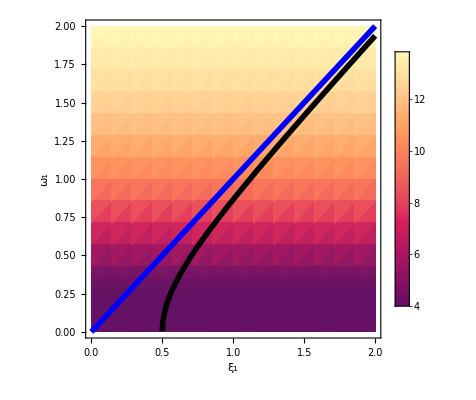

```mathematica
κ=1;
Show[DensityPlot[Fwn/.{κ->2},{ξ1,0,2},{ω1,0,2},PlotLegends->Automatic,FrameLabel->{"ξ_1","ω_1"},Exclusions->Automatic],Plot[1/2 √(-κ^2+4 Subscript[ξ, 1]^2)/.{κ->2},{Subscript[ξ, 1],0,2},AspectRatio->1,PlotRange->{0,2},PlotStyle->{Black,Thickness[0.01]}],Plot[Subscript[ξ, 1],{Subscript[ξ, 1],0,2},AspectRatio->1,PlotStyle->{Blue,Thickness[0.01]}]]
```

1.83303

3.66606

{(-1-2000 √(ξ_1^2-ω_1^2))/2000,(-1+2000 √(ξ_1^2-ω_1^2))/2000}

{(-0.917015+0. ⅈ)-√(1. ξ_1^2-1. ω_1^2),(-0.917015+0. ⅈ)+√(1. ξ_1^2-1. ω_1^2)}

{(-1.83353+0. ⅈ)-√(1. ξ_1^2-1. ω_1^2),(-1.83353+0. ⅈ)+√(1. ξ_1^2-1. ω_1^2)}

1/ξ1^2

0

0

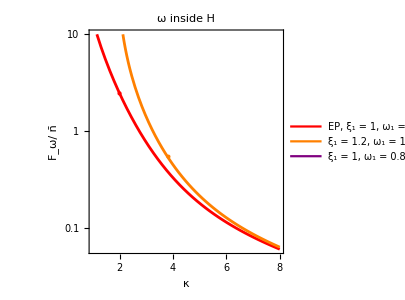

```mathematica
Clear[κ]
EP={ξ1->2,ω1->2};
aEP1={ξ1->2.2,ω1->2};
aEP2={ξ1->2,ω1->0.8};
ϵ=10^-3;
max=10^1;
kmax=8;

th1=2 Sqrt[ξ1^2-ω1^2]/.aEP1//N
th2=2 Sqrt[ξ1^2-ω1^2]/.aEP2//N

DM/.κ->2 Sqrt[ξ1^2-ω1^2]+ϵ/.EP//Eigenvalues
DM/.κ->2 Sqrt[ξ1^2-ω1^2]+ϵ/.aEP1//Eigenvalues
DM/.κ->2 Sqrt[ξ1^2-ω1^2]+ϵ/.aEP2//Eigenvalues


Limit[Fxn,κ->∞]
Limit[Fkn,κ->∞]
Limit[Fwn,κ->∞]

(*Show[LogPlot[{Fxn/.EP},{κ,0+ϵ,kmax},PlotRange->{0,max},PlotStyle->Red,
PlotLegends->Placed[LineLegend[{Red,Orange,Purple},{"EP, ξ_1 = 1, ω_1 = 1","ξ_1 = 1.1, ω_1 = 1","ξ_1 = 1, ω_1 = 0.8"},LabelStyle->{FontSize->10},LegendMargins->{{2,2},{2,2}},Spacings->{0.4,0.3},LegendFunction->(Framed[#,Background->White,FrameStyle->Black,FrameMargins->3]&)
],{Right,Top}]
],
LogPlot[{Fxn/.aEP1},{κ,th1+ϵ,kmax},PlotRange->{0,max},PlotStyle->Orange],
LogPlot[{Fxn/.aEP2},{κ,th2+ϵ,kmax},PlotRange->{0,max},PlotStyle->Purple],
Frame->True,FrameTicksStyle->Directive[FontSize->15],AspectRatio->1,FrameLabel->{Style["κ",18,Italic,FontFamily->"Arial"],Style[TraditionalForm["F_ξ/"Overscript["n","_"]],18,Italic,FontFamily->"Arial"]},FrameStyle->Directive[Black,Thickness[0.006]],ImageSize->300
]

Show[LogPlot[{Fkn/.EP},{κ,0+ϵ,kmax},PlotRange->{0,max},PlotStyle->Red,
PlotLegends->Placed[LineLegend[{Red,Orange,Purple},{"EP, ξ_1 = 1, ω_1 = 1","ξ_1 = 1.1, ω_1 = 1","ξ_1 = 1, ω_1 = 0.8"},LabelStyle->{FontSize->10},LegendMargins->{{2,2},{2,2}},Spacings->{0.4,0.3},LegendFunction->(Framed[#,Background->White,FrameStyle->Black,FrameMargins->3]&)
],{Right,Top}]
],
LogPlot[{Fkn/.aEP1},{κ,th1+ϵ,kmax},PlotRange->{0,max},PlotStyle->Orange],
LogPlot[{Fkn/.aEP2},{κ,th2+ϵ,kmax},PlotRange->{0,max},PlotStyle->Purple],
Frame->True,FrameTicksStyle->Directive[FontSize->15],AspectRatio->1,FrameLabel->{Style["κ",18,Italic,FontFamily->"Arial"],Style[TraditionalForm["F_κ/"Overscript["n","_"]],18,Italic,FontFamily->"Arial"]},FrameStyle->Directive[Black,Thickness[0.006]],ImageSize->300
]*)


Show[LogPlot[{Fwn/.EP},{κ,0+ϵ,kmax},PlotRange->{{1,kmax},{0,max}},PlotStyle->Red,
PlotLegends->Placed[LineLegend[{Red,Orange,Purple},{"EP, ξ_1 = 1, ω_1 = 1","ξ_1 = 1.2, ω_1 = 1","ξ_1 = 1, ω_1 = 0.8"},LabelStyle->{FontSize->10},LegendMargins->{{2,2},{2,2}},Spacings->{0.4,0.3},LegendFunction->(Framed[#,Background->White,FrameStyle->Black,FrameMargins->3]&)
],{Right,Top}]
],
LogPlot[{Fwn/.aEP1},{κ,th1+ϵ,kmax},PlotRange->{0,max},PlotStyle->Orange],
(*LogPlot[{Fwn/.aEP2},{κ,th2+ϵ,kmax},PlotRange->{0,max},PlotStyle->Purple],*)
Frame->True,FrameTicksStyle->Directive[FontSize->15],AspectRatio->1,FrameLabel->{Style["κ",18,Italic,FontFamily->"Arial"],Style[TraditionalForm["F_ω/"Overscript["n","_"]],18,Italic,FontFamily->"Arial"]},FrameStyle->Directive[Black,Thickness[0.006]],ImageSize->300,PlotLabel->"ω inside H",Epilog->{Red,PointSize[Large],Point[{2,0.9}],Orange,PointSize[Large],Point[{3.83,-0.6}]}
]
```

1.83303

3.66606

{(-1-2000 √(ξ_1^2-ω_1^2))/2000,(-1+2000 √(ξ_1^2-ω_1^2))/2000}

{(-0.917015+0. ⅈ)-√(1. ξ_1^2-1. ω_1^2),(-0.917015+0. ⅈ)+√(1. ξ_1^2-1. ω_1^2)}

{(-1.83353+0. ⅈ)-√(1. ξ_1^2-1. ω_1^2),(-1.83353+0. ⅈ)+√(1. ξ_1^2-1. ω_1^2)}

1/ξ1^2

0

0

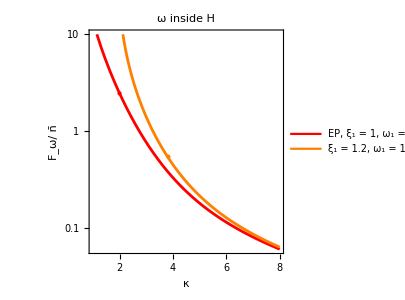

```mathematica
Clear[κ]
EP={ξ1->2,ω1->2};
aEP1={ξ1->2.2,ω1->2};
aEP2={ξ1->2,ω1->0.8};
ϵ=10^-3;
max=10^1;
kmax=8;

th1=2 Sqrt[ξ1^2-ω1^2]/.aEP1//N
th2=2 Sqrt[ξ1^2-ω1^2]/.aEP2//N

DM/.κ->2 Sqrt[ξ1^2-ω1^2]+ϵ/.EP//Eigenvalues
DM/.κ->2 Sqrt[ξ1^2-ω1^2]+ϵ/.aEP1//Eigenvalues
DM/.κ->2 Sqrt[ξ1^2-ω1^2]+ϵ/.aEP2//Eigenvalues


Limit[Fxn,κ->∞]
Limit[Fkn,κ->∞]
Limit[Fwn,κ->∞]

(*Show[LogPlot[{Fxn/.EP},{κ,0+ϵ,kmax},PlotRange->{0,max},PlotStyle->Red,
PlotLegends->Placed[LineLegend[{Red,Orange,Purple},{"EP, ξ_1 = 1, ω_1 = 1","ξ_1 = 1.1, ω_1 = 1","ξ_1 = 1, ω_1 = 0.8"},LabelStyle->{FontSize->10},LegendMargins->{{2,2},{2,2}},Spacings->{0.4,0.3},LegendFunction->(Framed[#,Background->White,FrameStyle->Black,FrameMargins->3]&)
],{Right,Top}]
],
LogPlot[{Fxn/.aEP1},{κ,th1+ϵ,kmax},PlotRange->{0,max},PlotStyle->Orange],
LogPlot[{Fxn/.aEP2},{κ,th2+ϵ,kmax},PlotRange->{0,max},PlotStyle->Purple],
Frame->True,FrameTicksStyle->Directive[FontSize->15],AspectRatio->1,FrameLabel->{Style["κ",18,Italic,FontFamily->"Arial"],Style[TraditionalForm["F_ξ/"Overscript["n","_"]],18,Italic,FontFamily->"Arial"]},FrameStyle->Directive[Black,Thickness[0.006]],ImageSize->300
]

Show[LogPlot[{Fkn/.EP},{κ,0+ϵ,kmax},PlotRange->{0,max},PlotStyle->Red,
PlotLegends->Placed[LineLegend[{Red,Orange,Purple},{"EP, ξ_1 = 1, ω_1 = 1","ξ_1 = 1.1, ω_1 = 1","ξ_1 = 1, ω_1 = 0.8"},LabelStyle->{FontSize->10},LegendMargins->{{2,2},{2,2}},Spacings->{0.4,0.3},LegendFunction->(Framed[#,Background->White,FrameStyle->Black,FrameMargins->3]&)
],{Right,Top}]
],
LogPlot[{Fkn/.aEP1},{κ,th1+ϵ,kmax},PlotRange->{0,max},PlotStyle->Orange],
LogPlot[{Fkn/.aEP2},{κ,th2+ϵ,kmax},PlotRange->{0,max},PlotStyle->Purple],
Frame->True,FrameTicksStyle->Directive[FontSize->15],AspectRatio->1,FrameLabel->{Style["κ",18,Italic,FontFamily->"Arial"],Style[TraditionalForm["F_κ/"Overscript["n","_"]],18,Italic,FontFamily->"Arial"]},FrameStyle->Directive[Black,Thickness[0.006]],ImageSize->300
]*)


Show[LogPlot[{Fwn/.EP},{κ,0+ϵ,kmax},PlotRange->{{1,kmax},{0,max}},PlotStyle->Red,
PlotLegends->Placed[LineLegend[{Red,Orange,Purple},{"EP, ξ_1 = 1, ω_1 = 1","ξ_1 = 1.2, ω_1 = 1"},LabelStyle->{FontSize->10},LegendMargins->{{2,2},{2,2}},Spacings->{0.4,0.3},LegendFunction->(Framed[#,Background->White,FrameStyle->Black,FrameMargins->3]&)
],{Right,Top}]
],
LogPlot[{Fwn/.aEP1},{κ,th1+ϵ,kmax},PlotRange->{0,max},PlotStyle->Orange],
(*LogPlot[{Fwn/.aEP2},{κ,th2+ϵ,kmax},PlotRange->{0,max},PlotStyle->Purple],*)
Frame->True,FrameTicksStyle->Directive[FontSize->15],AspectRatio->1,FrameLabel->{Style["κ",18,Italic,FontFamily->"Arial"],Style[TraditionalForm["F_ω/"Overscript["n","_"]],18,Italic,FontFamily->"Arial"]},FrameStyle->Directive[Black,Thickness[0.006]],ImageSize->300,PlotLabel->"ω inside H",Epilog->{Red,PointSize[Large],Point[{2,0.9}],Orange,PointSize[Large],Point[{3.83,-0.6}]}
]
```

```mathematica
Fwn/.EP/.κ->2//N
Fwn/.aEP1/.κ->2+th1//N
Fwn/.aEP2/.κ->2+th1//N
th1+2
```

2.46667

0.52945

2.07186

3.83303

Unset::norep: Assignment on Subscript for ξ_1 not found.

$Failed

Unset::norep: Assignment on Subscript for ω_1 not found.

$Failed

Eigensystem at EP

{{-κ/2,-κ/2},{{-ⅈ,1},{0,0}}}

Threshold

{{ξ_1→ConditionalExpression[-1/2 √(-Im[κ]^2+4 ω_1^2), ]},{ξ_1→ConditionalExpression[1/2 √(-Im[κ]^2+4 ω_1^2), ]},{ξ_1→ConditionalExpression[-1/2 √(κ^2+4 ω_1^2), Im[κ]==0&&Re[κ]<0]},{ξ_1→ConditionalExpression[1/2 √(κ^2+4 ω_1^2), Im[κ]==0&&Re[κ]<0]}}

(√(4+κ^2))/2

Eigensystem

{{-κ/2-√(ξ_1^2-ω_1^2),-κ/2+√(ξ_1^2-ω_1^2)},{{-(ⅈ ω_1+√(ξ_1^2-ω_1^2))/ξ_1,1},{(-ⅈ ω_1+√(ξ_1^2-ω_1^2))/ξ_1,1}}}

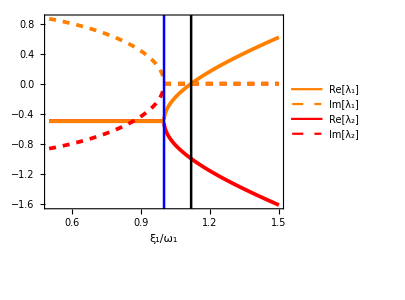

{{-1/2,-1/2},{{-ⅈ,1},{0,0}}}

{{-1,0},{{-(ⅈ √(1+4 ω_1^2))/(ⅈ+2 ω_1),1},{-(ⅈ √(1+4 ω_1^2))/(-ⅈ+2 ω_1),1}}}

```mathematica
Nmodes=1;
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Clear[κ]
Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]]//FullSimplify;

"Eigensystem at EP"
Eigensystem[EOM/.Subscript[ξ, 1]->Subscript[ω, 1]]
"Threshold"
Solve[-κ/2-√(Subscript[ξ, 1]^2-Subscript[ω, 1]^2)==0,Subscript[ξ, 1]]
1/2 √(κ^2+4 Subscript[ω, 1]^2)/.Subscript[ω, 1]->1

"Eigensystem "
eig=Eigensystem[EOM]//FullSimplify

κ=1;
Plot[Evaluate[{Re[eig[[1,1]]],Re[eig[[1,2]]],Im[eig[[1,1]]],Im[eig[[1,2]]]}/.Subscript[ω, 1]->1],{Subscript[ξ, 1],0.5,1.5},Axes->None,PlotStyle->{{Red,Thickness[0.009]},{Orange,Thickness[0.009]},{Red,Dashed,Thickness[0.009]},{Orange,Dashed,Thickness[0.009]}},Frame->True,FrameTicksStyle->Directive[FontSize->15],AspectRatio->1,FrameLabel->{Style["ξ_1/ω_1",18,Italic,FontFamily->"Arial"]},FrameStyle->Directive[Black,Thickness[0.006]],ImageSize->300,PlotLegends->Placed[LineLegend[{Orange,{Orange,Dashed},Red,{Red,Dashed}},{"Re[λ_1]","Im[λ_1]","Re[λ_2]","Im[λ_2]"},LabelStyle->{FontSize->10},LegendMargins->{{2,2},{2,2}},Spacings->{0.4,0.3},LegendFunction->(Framed[#,Background->White,FrameStyle->Black,FrameMargins->3]&)
],{Left,Bottom}],Epilog->{Directive[Blue,Thickness[0.006]],Line[{{1,-3},{1,3}}],Text[Style["EP",14,Blue,FontFamily->"Arial",Bold],{1.1,-2.5}],Directive[Black,Thickness[0.006]],Line[{{1/2 √(κ^2+4 Subscript[ω, 1]^2)/.Subscript[ω, 1]->1,-3},{1/2 √(κ^2+4 Subscript[ω, 1]^2)/.Subscript[ω, 1]->1,3}}],Text[Style["Threshold",14,Black,FontFamily->"Arial",Bold],{1.7,-1}]}]

Eigensystem[EOM/.Subscript[ξ, 1]->1/.Subscript[ω, 1]->1]
Eigensystem[EOM/.Subscript[ξ, 1]->1/2 √(κ^2+4 Subscript[ω, 1]^2)]
```

```mathematica
Limit[Fk,κ->∞]
Limit[Fw,κ->2 √(Subscript[ξ, 1]^2-Subscript[ω, 1]^2)]//FullSimplify
```

0

Indeterminate

```mathematica
"QFI at stability"
F/.Subscript[ξ, 1]->Sqrt[Subscript[ω, 1]^2+κ^2/4]//FullSimplify


"mean photon at stability"
n/.κ->2 √(Subscript[ξ, 1]^2-Subscript[ω, 1]^2)//FullSimplify

"QFI normalized to mean"
Fn=F/n//FullSimplify
"QFI normalized at stability"
F/n/.Subscript[ξ, 1]->Sqrt[Subscript[ω, 1]^2+κ^2/4]//FullSimplify


"QFI at EP"
F/n/.Subscript[ξ, 1]->Subscript[ω, 1]//FullSimplify
"n at EP"
n/.Subscript[ξ, 1]->Subscript[ω, 1]//FullSimplify

"EP"
F/n/.Subscript[ξ, 1]->1/.κ->2/.Subscript[ω, 1]->1//N
F/.{Subscript[ξ, 1]->1,κ->2,Subscript[ω, 1]->1}//N
n/.{Subscript[ξ, 1]->1,κ->2,Subscript[ω, 1]->1}//N


"Above EP"
F/n/.Subscript[ξ, 1]->1.3/.κ->2/.Subscript[ω, 1]->1//N
F/.{Subscript[ξ, 1]->1.3,κ->2,Subscript[ω, 1]->1}
n/.{Subscript[ξ, 1]->1.3,κ->2,Subscript[ω, 1]->1}



"At Threshold"
F/n/.Subscript[ξ, 1]->Sqrt[Subscript[ω, 1]^2+1]/.κ->2/.Subscript[ω, 1]->1//FullSimplify
F/.Subscript[ξ, 1]->Sqrt[Subscript[ω, 1]^2+1]/.κ->2/.Subscript[ω, 1]->1
n/.Subscript[ξ, 1]->Sqrt[Subscript[ω, 1]^2+1]/.κ->2/.Subscript[ω, 1]->1
Eigensystem[DM/.Subscript[ξ, 1]->Sqrt[Subscript[ω, 1]^2+1]/.κ->2/.Subscript[ω, 1]->1]
```